# Applications of the Singular Value Decomposition (SVD)

## SVD: What is it

The Singular Value Decomposition (SVD) SVD factors a matrix A∈ℝ^(m×n) into the useful product of structured matrices
	A=U.Σ.Vᵀ=∑_(i=1)^r σ_i u_i⊗v_i  
where U∈ℝ^(m×m) and V∈ℝ^(n×n) are orthogonal and the inner matrix Σ∈ℝ^(m×n) is diagonal with non-increasing and  non-negative entries.  The diagonal entries σ_i=Σ_(i,i) for 1≤i≤min(m,n) are called singular values and σ_1≥σ_i≥σ_(i+1)≥σ_(min(m,n))≥0. The rank r of A is the number of non-zero singular values and r≤min(m,n). The ordering of the singular values means that σ_r>σ_(r+1)=0. The columns u_i of U=(u_1 u_2(…u)_m) are left singular vectors of A. The columns v_i of V=(v_1 v_2(…v)_n) are right singular vectors of A.

The SVD is tells you everything about the matrix.  It is expensive to compute the complete SVD.     Lots of measures of the size of a matrix can be computed from the SVD.

The Frobenius norm of A ||A(||)_F=√(∑_(i=1)^m ∑_(j=1)^n|a_(i,j)|^2)=√(∑_(i=1)^(min(m,n)) σ_i^2)

The operator 2 norm of A ||A(||)_2= min_(||x||=1) ||A x(||)_2=σ_1

The nuclear norm of A ||A(||)_*= ∑_(i=1)^(min(m,n)) σ_i

The rank of

The SVD give the best rank k approximation to the matrix A in both the operator and Frobenius norms is A_(k)=∑_(i=1)^k σ_i u_i⊗v.  In symbols
	A_(k)=argmin_(rank(B)≤k)||A-B(||)_F  with min_(rank(B)≤k) ||A-B(||)_F^2=∑_(i=k+1)^r σ_i^2
and
	A_(k)=argmin_(rank(B)≤k)||A-B(||)_2 with min_(rank(B)≤k) ||A-B(||)_2=σ_(k+1)

The SVD give the best rank k approximation to the matrix A in both the operator and Frobenius norms is A_(k)=∑_(i=1)^k σ_i u_i⊗v.  In symbols
	A_(k)=argmin_(rank(B)≤k)||A-B(||)_F  with min_(rank(B)≤k) ||A-B(||)_F^2=∑_(i=k+1)^r σ_i^2
and
	A_(k)=argmin_(rank(B)≤k)||A-B(||)_2 with min_(rank(B)≤k) ||A-B(||)_2=σ_(k+1)

## SVD: What does it mean

The SVD expresses any matrix as a rotation (called V) of the input space followed by stretches (described by the singular values σ_i) in simple directions and then finish off with a rotation (called U) of the output space.  Informally as long as we are prepared to not worry about rotations of the input and output spaces every matrix is diagonal!  Diagonal matrices are easy! Rotations are really just a choice of coordinate system.

## SVD: Why is it so useful.

The rotations U and V are really just a choice of coordinate system for the input and output spaces.   The SVD lets us choose useful coordinate systems that identify the most important parts of a matrix. Lets think about the streaming service Pandora and the Music Genome Project and me. According to wiki https://en.wikipedia.org/wiki/Music_Genome_Project the Music Genome project assigns a vector to every song consisting of up to 450 genes.  Pandora learns which music you like by the songs you let play and/or the songs/artists you request.

I am going to imagine that Pandora has collected a bunch of vectors that I like.  I have a bunch (say a few thousand) vectors of length 450.  I am going to think of this as a matrix A∈ℝ^(450×1000).  Now I like British punk rock, New York proto punk, some new wave, classical guitar music, classic rock, very early electronic music, traditional reggae, Nigerian Juju, classical horn works, and a bunch of other specific artists. This information should be buried in the data that Pandora has collected!

So I do an SVD on the my 450×1000 matrix and look at the singular values.  It is very common to see a few larger singular values with a clear break and all the remaining singular values being small. Suppose the 5 largest singular values capture 95% of the matrix then it is pretty clear that
	A_(5)=∑_(i=1)^5 σ_i u_i⊗v_i	
summarizes my musical tastes.  In this example u_1,u_2,…,u_5 represent the genome of types of music that I like and σ_1,σ_2,…,σ_5 represents how much I like that music.

It is VERY unlikely that u_1 is an identifiable type of music.  Deep Purple did not record a lot of Nigerian Juju on early synthesizers with a reggae beat!  The vector u_1 will have negative entries. The Music Genome Project assigns values between 0 and 5 in half unit increments to each “gene”. It is not clear what a negative entry means!

## Image Compression

```mathematica
ImageColorSpace[ExampleData[{"TestImage","House"}]]
```

RGB

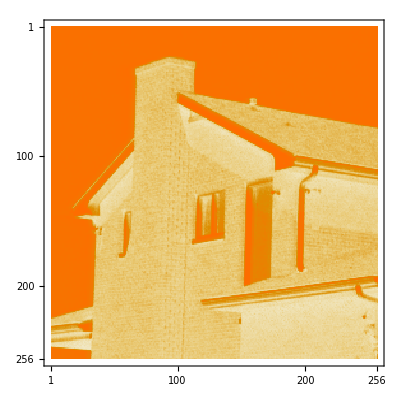

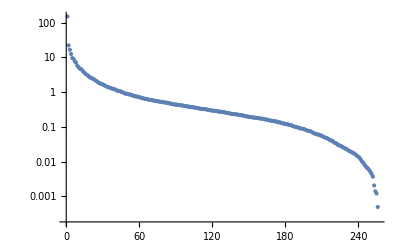

```mathematica
Pic=ImageData[ExampleData[{"TestImage","House"}]]⟦All,All,3⟧;
MatrixPlot[Pic]
ListLogPlot[SingularValueList[Pic],PlotRange->All]
```

{{256,256},{256,256},{256,256}}

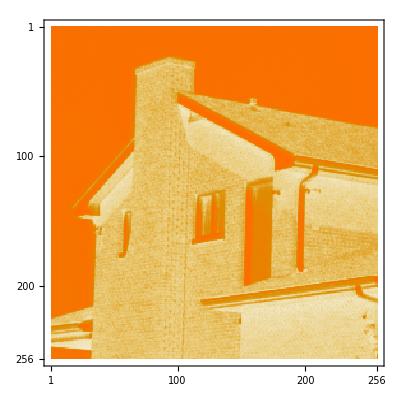

```mathematica
{U,S,V}=SingularValueDecomposition[Pic];
Map[Dimensions,{U,S,V}]
NewPic=U.S.Vᵀ;
MatrixPlot[NewPic]
```

{{23,23},{23,34},{34,34}}

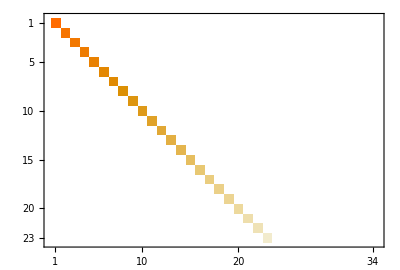

```mathematica
{m,n}={23,34};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
Map[Dimensions,{U,S,V}]
MatrixPlot[S]
```

{{123,123},{123,34},{34,34}}

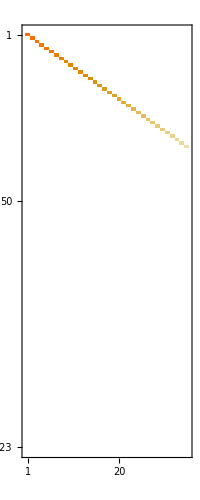

```mathematica
{m,n}={123,34};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
Map[Dimensions,{U,S,V}]
MatrixPlot[S]
```

```mathematica
Black and white etst image
```

```mathematica
A= Import["https://www.google.com/url?sa=i&url=https%3A%2F%2Fopenaccess.thecvf.com%2Fcontent%2FWACV2021%2Fsupplemental%2FKoh_Text-to-Image_Generation_Grounded_WACV_2021_supplemental.pdf&psig=AOvVaw1vnmDnOnrNOZvnsoTqhp_e&ust=1697211986952000&source=images&cd=vfe&opi=89978449&ved=0CBAQjRxqFwoTCIDNgMPt8IEDFQAAAAAdAAAAABAD"]
```

Redirect Notice
The previous page is sending you to https://openaccess.thecvf.com/content/WACV2021/supplemental/Koh_Text-to-Image_Generation_Grounded_WACV_2021_supplemental.pdf .

If you do not want to visit that page, you can return to the previous page .

{a, da} + {b, db} = {a + b, da + db}
{a, da}*{b, db} = {a*b, a*db + da*b}
Sin[{a,da}] = {Sin[a], Cos[a] da}
Cos[{a,da}] = {Cos[a], -Sin[a] da}
ArcTan[{a,da}] = {ArcTan[a],  da/(1+a^2)}
Exp[{a,da}] = {Exp[a],  da}
Plus a ton of diff rules! Cos, Sin

```mathematica
D[x^3,x]
D[Exp[x],x]
D[Log[x],x]
```

3 x^2

ⅇ^x

1/x